Copyright (C) 2016 Leo Fang <leofang@phy.duke.edu>

This program is free software. It comes without any warranty, to the extent permitted by applicable law. You can redistribute it and/or modify it under the terms of the WTFPL, Version 2, as published by Sam Hocevar. See the accompanying LICENSE file or http://www.wtfpl.net/ for more details.

In this notebook, using the sample file k0a_0.5pi_on_new as an example, I demonstrate how to perform post-processing of the results generated by the FDTD code.

```mathematica
(* read input parameters *)
Import[NotebookDirectory[]<>"../k0a_0.5pi_on_new"]
```

```mathematica
(* set the input parameters in the corresponding symbols *)
%//ToExpression;
```

```mathematica
(* setup based on input parameters *)
Xmin=-(Nx+nx+1)Delta;
Xmax=(Nx)Delta;
qubit1=-nx/2*Delta;
qubit2=nx/2*Delta;
```

```mathematica
(* read the absolute value of the computed two-photon wavefunction *)
χ=ReadList[NotebookDirectory[]<>"../k0a_0.5pi_on_new.abs_chi.out",Number,RecordLists->True];
```

```mathematica
(* plot Subscript[g, 2](τ,t)=|χ(a+Δ,a+Δ+τ,t)|^2 as an animation in time t *)
Manipulate[ListPlot[χ[[i]]^2,Joined->True,PlotMarkers->None,DataRange->{0,(Nx-nx/2+1)Delta*gamma},PlotRange->{0,All},GridLines->{{(qubit2-qubit1)*gamma},None},
PlotLabel->"t="<>ToString[(Nx+nx/2+1)+(Tstep+1)(i-1)]<>"Δ",AxesLabel->{"Γτ","g_2(τ,t)"}],{i,1,Length[χ],1}]
```

```mathematica
(* plot Subscript[g, 2](τ,t)=|χ(a+Δ,a+Δ+τ,t)|^2 at the last snapshot *)
ListPlot[χ[[-1]]^2,Joined->True,DataRange->{0,(Nx-nx/2+1)Delta*gamma},PlotRange->{0,All},GridLines->{{(qubit2-qubit1)*gamma},None},AxesLabel->{"Γτ","g_2(τ)"}]
```

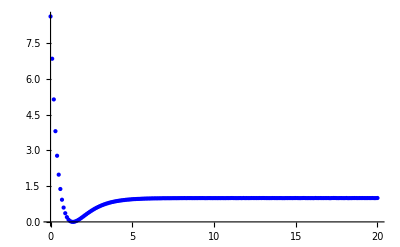
```mathematica
(* Compare with the result obtained using scattering theory; see PRA 91,053845 (2015) *)
Show[%,-Graphics-]
```

```mathematica
(* the next file is memory consuming, so clear some memory first *)
Clear[χ]
```

```mathematica
(* read computed wavefunctions *)
bR=ReadList[NotebookDirectory[]<>"../k0a_0.5pi_on_new.re.out",Number,RecordLists->True](* real part*);
bI=ReadList[NotebookDirectory[]<>"../k0a_0.5pi_on_new.im.out",Number,RecordLists->True](* imaginary part*);
```

```mathematica
(* construct the wavefunction *)
ψ=bR+I*bI;
```

```mathematica
(* set the fraction (10%) for plotting blow *)
ny=1/10;
```

```mathematica
(* plot the real part of the first 10% (in time) solution *)
ListDensityPlot[bR[[1;;Ceiling[ny*Length[bR]]]],DataRange->{{qubit1,Xmax},{0,(Ceiling[ny*Length[bR]]-1)*(Tstep+1)*Delta}},PlotRange->All,ColorFunction->"Warm",PlotLegends->Automatic,AspectRatio->Automatic,MaxPlotPoints->200]
```

```mathematica
(* plot the absolute value square of the first 10% (in time) solution *)
ListDensityPlot[Abs[ψ[[1;;Ceiling[ny*Length[bR]]]]]^2,DataRange->{{qubit1,Xmax},{0,(Ceiling[ny*Length[bR]]-1)*(Tstep+1)*Delta}},PlotRange->All,ColorFunction->"Warm",PlotLegends->Automatic,AspectRatio->Automatic,MaxPlotPoints->200]
```

```mathematica
(* plot the real part of the entire solution *)
ListDensityPlot[bR,DataRange->{{qubit1,Xmax},{0,(Length[bR]-1)*(Tstep+1)*Delta}},PlotRange->All,ColorFunction->"Warm",PlotLegends->Automatic,AspectRatio->Automatic,MaxPlotPoints->200]
```

```mathematica
(* plot the absolute value square of the entire solution *)
ListDensityPlot[Abs[ψ]^2,DataRange->{{qubit1,Xmax},{0,(Length[bR]-1)*(Tstep+1)*Delta}},PlotRange->All,ColorFunction->"Warm",PlotLegends->Automatic,AspectRatio->Automatic,MaxPlotPoints->200]
```

```mathematica
(* show the propagation of the real part of the wave as an animation *)
Manipulate[ListPlot[bR[[i]],Joined->True,DataRange->{qubit1,Xmax},PlotRange->{All,{-8,8}},GridLines->{{qubit1,qubit2},None},
PlotLabel->"t="<>ToString[(Tstep+1)(i-1)]<>"Δ",AxesLabel->{"x","Re[ψ(x,t)]"}],{i,1,Length[bR],1}]
```

```mathematica
(* show the propagation of the absolute value of the wave as an animation *)
Manipulate[ListPlot[Abs@ψ[[i]],Joined->True,DataRange->{qubit1,Xmax},PlotRange->{All,{0,7.5}},GridLines->{{qubit1,qubit2},None},
PlotLabel->"t="<>ToString[(Tstep+1)(i-1)]<>"Δ",AxesLabel->{"x","Re[ψ(x,t)]"}],{i,1,Length[bR],1}]
```